```mathematica
Needs["nlchains`"];
```

```mathematica
(*adjust this accordingly*)
SetDirectory["path/to/unzipped/supporting/material"]
```

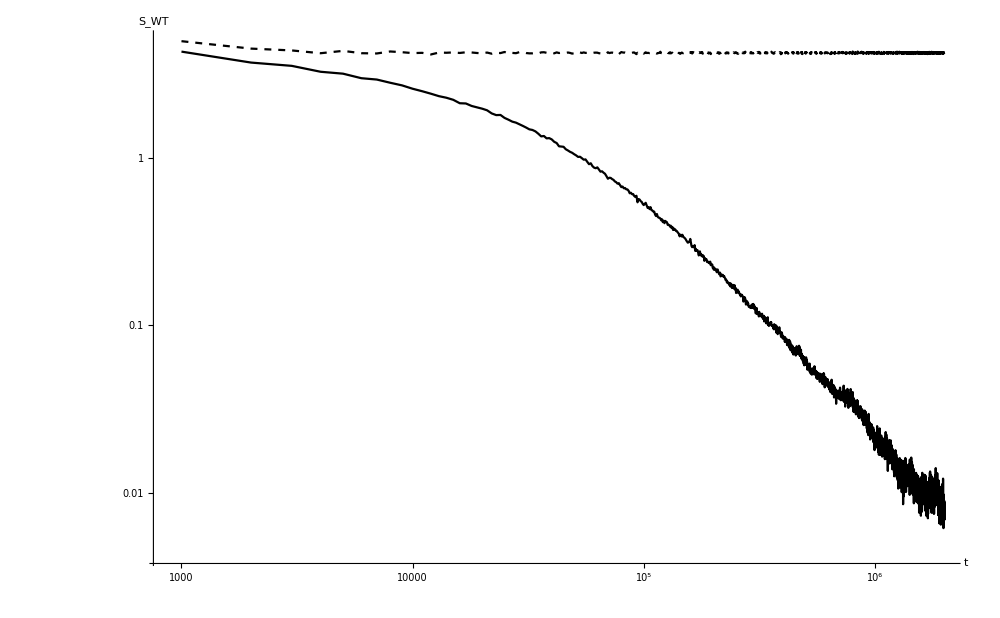

```mathematica
LoadEntropy["toda-fputalpha/fput-entropy"];
LoadEntropy["toda-fputalpha/toda-entropy"];
ListLogLogPlot[{%%[[All,;;2]],%[[All,;;2]]},PlotRange->Full,AxesLabel->{"t","S_WT"},BaseStyle->Large,ImageSize->1000,PlotStyle->{Black,Directive[Black,Dashed]},Joined->True]
```

```mathematica
{"toda-fputalpha/fput-linenergies-0","toda-fputalpha/fput-linenergies-20000000","toda-fputalpha/toda-linenergies-20000000"};
ListPlot[Rest@LoadLinearEnergies[#]&/@%,PlotRange->Full,ImageSize->1000,BaseStyle->Large,AxesLabel->{"k","e_k"},PlotStyle->Black,PlotMarkers->{"○","●","■"}]
```

-Graphics-

```mathematica
scalingFPUT=With[{t0=EnergyFPUT[#,0.1,0.1]&/@LoadDump["FPUT-alpha0.1-beta0.1-t100000/dt0.01-0",64]},
With[{tfin=EnergyFPUT[#,0.1,0.1]&/@LoadDump[StringTemplate["FPUT-alpha0.1-beta0.1-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.2,0.5}
]
```

{{0.01,1.57133×10^-13},{0.02,6.28441×10^-13},{0.05,1.51142×10^-10},{0.1,9.74944×10^-9},{0.2,6.35596×10^-7},{0.5,0.000189285}}

```mathematica
scalingToda=With[{t0=EnergyToda[#,0.1]&/@LoadDump["Toda-alpha0.1-t100000/dt0.01-0",64]},
With[{tfin=EnergyToda[#,0.1]&/@LoadDump[StringTemplate["Toda-alpha0.1-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.2,0.5}
]
```

{{0.01,1.61431×10^-13},{0.02,5.86254×10^-13},{0.05,1.40844×10^-10},{0.1,9.21303×10^-9},{0.2,6.44791×10^-7},{0.5,0.000218467}}

```mathematica
scalingDNKG=With[{t0=EnergyDNKG[#,1,1]&/@LoadDump["KG-m1-beta1-t100000/dt0.01-0",64]},
With[{tfin=EnergyDNKG[#,1,1]&/@LoadDump[StringTemplate["KG-m1-beta1-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.2,0.5}
]
```

{{0.01,9.95761×10^-14},{0.02,1.32634×10^-12},{0.05,3.19044×10^-10},{0.1,2.08335×10^-8},{0.2,1.34547×10^-6},{0.5,0.000414618}}

```mathematica
Import["rKG-beta1-t100000/KGr64-1-3","Real64"];
scalingdDNKG=With[{t0=EnergydDNKG[#,%,1]&/@LoadDump["rKG-beta1-t100000/dt0.01-0",64]},
With[{tfin=EnergydDNKG[#,%,1]&/@LoadDump[StringTemplate["rKG-beta1-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.2,0.5}
]
```

{{0.01,1.02406×10^-13},{0.02,2.5518×10^-12},{0.05,6.23567×10^-10},{0.1,4.08698×10^-8},{0.2,2.78687×10^-6},{0.5,0.000877515}}

```mathematica
scalingDNLS=With[{t0=EnergyDNLS[#,0.1]&/@LoadComplexDump["DNLS-beta0.1-t100000/dt0.01-0",64]},
With[{tfin=EnergyDNLS[#,0.1]&/@LoadComplexDump[StringTemplate["DNLS-beta0.1-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.5}
]
```

{{0.01,8.6884×10^-9},{0.02,4.18089×10^-9},{0.05,1.76909×10^-9},{0.1,8.×10^-10},{0.11,7.69946×10^-10},{0.12,7.54426×10^-10},{0.13,9.93421×10^-10},{0.14,1.32431×10^-9},{0.15,1.92499×10^-9},{0.16,2.79859×10^-9},{0.17,4.03399×10^-9},{0.18,5.64646×10^-9},{0.19,7.85557×10^-9},{0.2,1.07572×10^-8},{0.5,3.94751×10^-6}}

```mathematica
scalingDNLSlinear=With[{t0=EnergyDNLS[#,0]&/@LoadComplexDump["DNLS-beta0-t100000/dt0.01-0",64]},
With[{tfin=EnergyDNLS[#,0]&/@LoadComplexDump[StringTemplate["DNLS-beta0-t100000/dt``-``"][NumberForm[#,{2,2}],Round[100000/#]],64]},{#,Abs[tfin-t0]/t0//Mean}]&/@{0.01,0.02,0.05,0.1,0.2,0.5}
]
```

{{0.01,8.59772×10^-9},{0.02,4.2645×10^-9},{0.05,1.77742×10^-9},{0.1,8.88713×10^-10},{0.2,4.28917×10^-10},{0.5,1.7378×10^-10}}

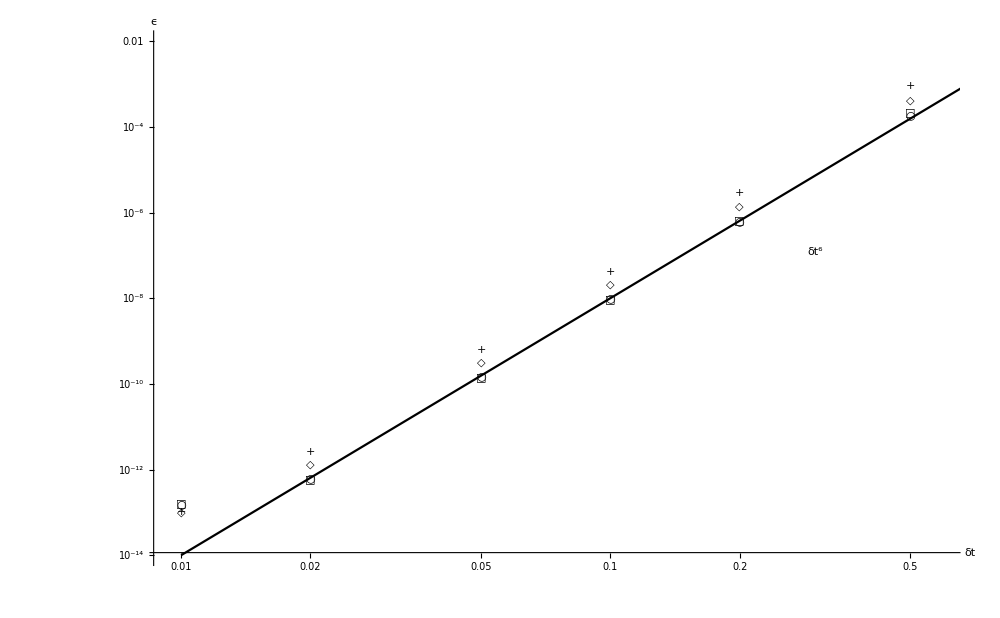

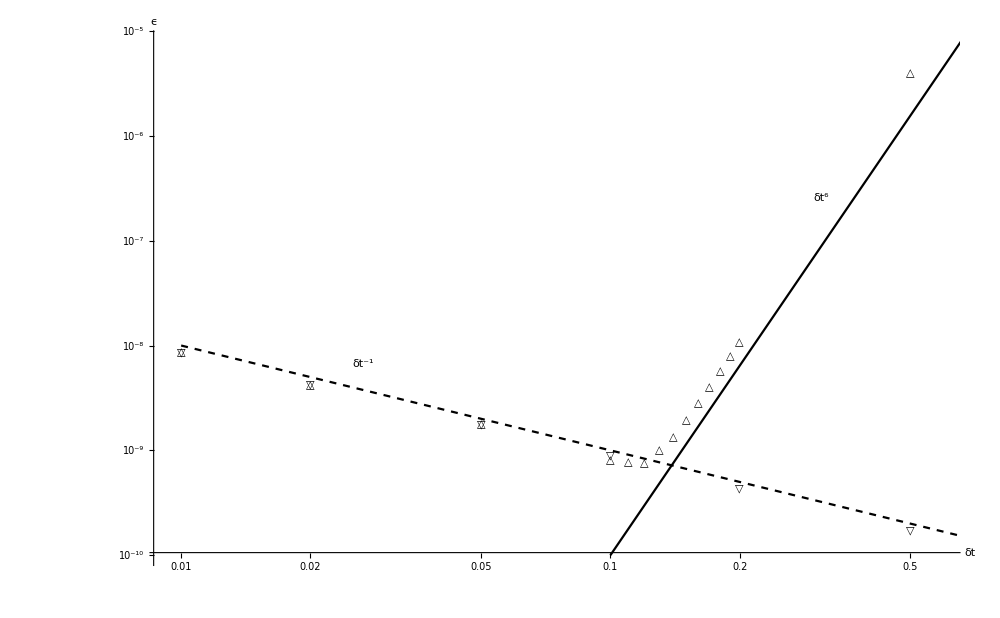

```mathematica
Show[ListLogLogPlot[{scalingFPUT,scalingToda,scalingDNKG,scalingdDNKG},PlotMarkers->{"○","□","◇","+"},PlotStyle->Black,PlotRange->{{Automatic,0.6},{1*^-14,1*^-2}}],LogLogPlot[Labeled[1*^-2δt^6,"δt^6",{0.3,Below}],{δt,0.01,10},PlotStyle->Black],BaseStyle->Large,AxesLabel->{"δt","ϵ"},ImageSize->1000]
Show[ListLogLogPlot[{scalingDNLS,scalingDNLSlinear},PlotMarkers->{"△","▽"},PlotStyle->Black,PlotRange->{{Automatic,0.6},{1*^-10,0.8*^-5}}],LogLogPlot[{Labeled[1*^-4δt^6,"δt^6",Scaled[0.6]],Labeled[1*^-10δt^-1,"δt^-1",Scaled[0.2]]},{δt,0.01,10},PlotStyle->{Black,Directive[Black,Dashed]},PlotRange->{{Automatic,0.6},{1*^-10,0.8*^-5}}],BaseStyle->Large,AxesLabel->{"δt","ϵ"},ImageSize->1000]
```